## Задача 1. а)

```mathematica
(* a=5 b=7*)
```

```mathematica
f[x_]:=(50(5+2)Sin [x]+x^3+33)/((7+2)+x^2)
f[x]
```

(33+x^3+350 Sin[x])/(9+x^2)

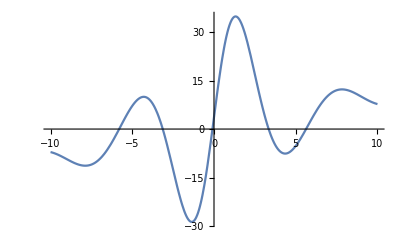

```mathematica
Plot[f[x],{x,-10,10}]
```

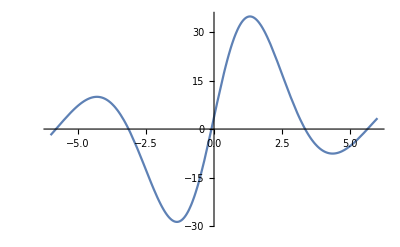

```mathematica
Plot[f[x],{x,-6,6}]
```

## б)

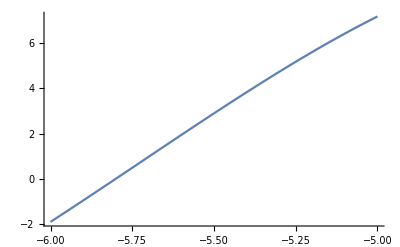

```mathematica
Plot[f[x],{x,-6,-5}]
```

```mathematica
f[-6.]
```

-1.89344

```mathematica
f[-5.]
```

7.1654

## в).

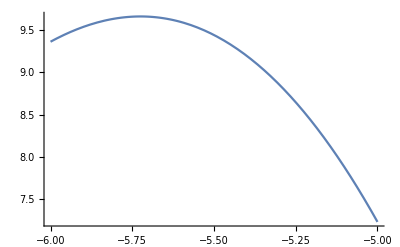

```mathematica
Plot[f'[x],{x,-6,-5}]
```

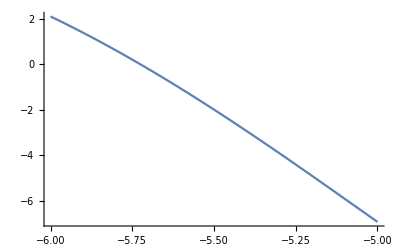

```mathematica
Plot[f''[x],{x,-6,-5}]
```

## г).

```mathematica
p=-6.
x0=-5.
```

-6.

-5.

## д).

```mathematica
For[n=0,n<=50,n++,
x1=x0-f[x0]/(f[x0]-f[p])*(x0-p);
Print["n = ",n,"x_n = ",x1];
x0=x1
]
```

n = 0x_n = -5.79098

n = 1x_n = -5.80133

n = 2x_n = -5.80121

n = 3x_n = -5.80121

n = 4x_n = -5.80121

n = 5x_n = -5.80121

n = 6x_n = -5.80121

n = 7x_n = -5.80121

n = 8x_n = -5.80121

n = 9x_n = -5.80121

n = 10x_n = -5.80121

n = 11x_n = -5.80121

n = 12x_n = -5.80121

n = 13x_n = -5.80121

n = 14x_n = -5.80121

n = 15x_n = -5.80121

n = 16x_n = -5.80121

n = 17x_n = -5.80121

n = 18x_n = -5.80121

n = 19x_n = -5.80121

n = 20x_n = -5.80121

n = 21x_n = -5.80121

n = 22x_n = -5.80121

n = 23x_n = -5.80121

n = 24x_n = -5.80121

n = 25x_n = -5.80121

n = 26x_n = -5.80121

n = 27x_n = -5.80121

n = 28x_n = -5.80121

n = 29x_n = -5.80121

n = 30x_n = -5.80121

n = 31x_n = -5.80121

n = 32x_n = -5.80121

n = 33x_n = -5.80121

n = 34x_n = -5.80121

n = 35x_n = -5.80121

n = 36x_n = -5.80121

n = 37x_n = -5.80121

n = 38x_n = -5.80121

n = 39x_n = -5.80121

n = 40x_n = -5.80121

n = 41x_n = -5.80121

n = 42x_n = -5.80121

n = 43x_n = -5.80121

n = 44x_n = -5.80121

n = 45x_n = -5.80121

n = 46x_n = -5.80121

n = 47x_n = -5.80121

n = 48x_n = -5.80121

n = 49x_n = -5.80121

n = 50x_n = -5.80121

```mathematica
m1=Abs[f'[-5.]]
```

7.2334

```mathematica
M1=Abs[f'[-6.]]
```

9.36308

```mathematica
R=(M1-m1)/m1
```

0.294422

```mathematica
f[x_]:=(33+x^3+350 Sin[x])/(9+x^2)
x0=-5.; p=-6.;
M1=Abs[f'[-6.]];
m1=Abs[f'[-5.]];
R=(M1-m1)/m1;
For[n=0,n<=10,n++,
x1=x0-f[x0]/(f[x0]-f[p])*(x0-p);
Print["n = ",n,"x_n = ",x1,"f(x_n) = ",f[x1],"ϵ_n = ",eps=R*Abs[x1-x0]];
x0=x1
]
```

n = 0x_n = -5.79098f(x_n) = 0.098616ϵ_n = 0.232883

n = 1x_n = -5.80133f(x_n) = -0.0011399ϵ_n = 0.00304646

n = 2x_n = -5.80121f(x_n) = 0.0000135054ϵ_n = 0.000035235

n = 3x_n = -5.80121f(x_n) = -1.59965×10^-7ϵ_n = 4.17458×10^-7

n = 4x_n = -5.80121f(x_n) = 1.89472×10^-9ϵ_n = 4.9446×10^-9

n = 5x_n = -5.80121f(x_n) = -2.24467×10^-11ϵ_n = 5.85669×10^-11

n = 6x_n = -5.80121f(x_n) = 2.63201×10^-13ϵ_n = 6.93757×10^-13

n = 7x_n = -5.80121f(x_n) = -1.99899×10^-15ϵ_n = 8.10647×10^-15

n = 8x_n = -5.80121f(x_n) = -1.99899×10^-15ϵ_n = 0.

n = 9x_n = -5.80121f(x_n) = -1.99899×10^-15ϵ_n = 0.

n = 10x_n = -5.80121f(x_n) = -1.99899×10^-15ϵ_n = 0.

## е).

```mathematica
f[x_]:=(33+x^3+350 Sin[x])/(9+x^2)
a=-6.; b=-5.;
For[n=0,n<=20,n++,
Print["n = ",n,"a_n = ",a,"b_n = ",b,"m_n = ",m=(a+b)/2,"f(m_n) = ",f[m],"ϵ_n = ",(b-a)/2];
If[f[m]>0,b=m,a=m]
]
```

n = 0a_n = -6.b_n = -5.m_n = -5.5f(m_n) = 2.89335ϵ_n = 0.5

n = 1a_n = -6.b_n = -5.5m_n = -5.75f(m_n) = 0.494224ϵ_n = 0.25

n = 2a_n = -6.b_n = -5.75m_n = -5.875f(m_n) = -0.708912ϵ_n = 0.125

n = 3a_n = -5.875b_n = -5.75m_n = -5.8125f(m_n) = -0.108734ϵ_n = 0.0625

n = 4a_n = -5.8125b_n = -5.75m_n = -5.78125f(m_n) = 0.192519ϵ_n = 0.03125

n = 5a_n = -5.8125b_n = -5.78125m_n = -5.79688f(m_n) = 0.0418205ϵ_n = 0.015625

n = 6a_n = -5.8125b_n = -5.79688m_n = -5.80469f(m_n) = -0.0334767ϵ_n = 0.0078125

n = 7a_n = -5.80469b_n = -5.79688m_n = -5.80078f(m_n) = 0.00416714ϵ_n = 0.00390625

n = 8a_n = -5.80469b_n = -5.80078m_n = -5.80273f(m_n) = -0.014656ϵ_n = 0.00195313

n = 9a_n = -5.80273b_n = -5.80078m_n = -5.80176f(m_n) = -0.00524473ϵ_n = 0.000976563

n = 10a_n = -5.80176b_n = -5.80078m_n = -5.80127f(m_n) = -0.000538872ϵ_n = 0.000488281

n = 11a_n = -5.80127b_n = -5.80078m_n = -5.80103f(m_n) = 0.00181412ϵ_n = 0.000244141

n = 12a_n = -5.80127b_n = -5.80103m_n = -5.80115f(m_n) = 0.000637617ϵ_n = 0.00012207

n = 13a_n = -5.80127b_n = -5.80115m_n = -5.80121f(m_n) = 0.0000493716ϵ_n = 0.0000610352

n = 14a_n = -5.80127b_n = -5.80121m_n = -5.80124f(m_n) = -0.00024475ϵ_n = 0.0000305176

n = 15a_n = -5.80124b_n = -5.80121m_n = -5.80122f(m_n) = -0.0000976895ϵ_n = 0.0000152588

n = 16a_n = -5.80122b_n = -5.80121m_n = -5.80122f(m_n) = -0.000024159ϵ_n = 7.62939×10^-6

n = 17a_n = -5.80122b_n = -5.80121m_n = -5.80121f(m_n) = 0.0000126063ϵ_n = 3.8147×10^-6

n = 18a_n = -5.80122b_n = -5.80121m_n = -5.80121f(m_n) = -5.77633×10^-6ϵ_n = 1.90735×10^-6

n = 19a_n = -5.80121b_n = -5.80121m_n = -5.80121f(m_n) = 3.41498×10^-6ϵ_n = 9.53674×10^-7

n = 20a_n = -5.80121b_n = -5.80121m_n = -5.80121f(m_n) = -1.18067×10^-6ϵ_n = 4.76837×10^-7

## ж).

```mathematica
(*Сравнение на двата метода*)
```

```mathematica
Log2[(-5-(-6))/0.0001]-1
```

12.2877

```mathematica
(*По метода на разполовяването са необходими 16 итерации за достигане на истинската точност. По метода на хордите са необходими 3 итерации.Метода на хордите е по-ефективен*)
```

## Задача 2.

```mathematica
A=({{1, 5-1, 3, 0}, {4, 2, 7, -2}, {0, 1, 1, 4}, {-(7+2), 2, 3, 5}})
```

{{1,4,3,0},{4,2,7,-2},{0,1,1,4},{-9,2,3,5}}

```mathematica
Length[A]
```

4

```mathematica
A[[1]]=A[[1]]/A[[1,1]]
```

{1,4,3,0}

```mathematica
A⟦2⟧=A⟦2⟧-A⟦2,1⟧*A⟦1⟧
```

{0,-14,-5,-2}

```mathematica
A⟦3⟧=A⟦3⟧-A⟦3,1⟧*A⟦1⟧
```

{0,1,1,4}

```mathematica
A//MatrixForm
```

(1 | 4 | 3 | 0
0 | -14 | -5 | -2
0 | 1 | 1 | 4
-9 | 2 | 3 | 5)

```mathematica
(*първи етап-получаваме единица на мястото на главния елемент а22=1)
```

```mathematica
A[[2]]=A[[2]]/A[[2,2]]
```

{0,1,5/14,1/7}

```mathematica
A//MatrixForm
```

(1 | 4 | 3 | 0
0 | 1 | 5/14 | 1/7
0 | 1 | 1 | 4
-9 | 2 | 3 | 5)

```mathematica
(*втори етап-получаване на нули във всички останали елементи от стълба*)
```

```mathematica
A⟦1⟧=A⟦1⟧-A⟦1,2⟧*A⟦2⟧
```

{1,0,11/7,-4/7}

```mathematica
A⟦3⟧=A⟦3⟧-A⟦3,2⟧*A⟦2⟧
```

{0,0,9/14,27/7}

```mathematica
A//MatrixForm
```

(1 | 0 | 11/7 | -4/7
0 | 1 | 5/14 | 1/7
0 | 0 | 9/14 | 27/7
-9 | 2 | 3 | 5)

```mathematica
(*първи етап-получаваме единица на мястото на главния елемент а33=1*)
```

```mathematica
A[[3]]=A[[3]]/A[[3,3]]
```

{0,0,1,6}

```mathematica
A//MatrixForm
```

(1 | 0 | 11/7 | -4/7
0 | 1 | 5/14 | 1/7
0 | 0 | 1 | 6
-9 | 2 | 3 | 5)

```mathematica
(*втори етап-получаване на нули във всички останали елементи от стълба*)
```

```mathematica
A⟦1⟧=A⟦1⟧-A⟦1,3⟧*A⟦3⟧
```

{1,0,0,-10}

```mathematica
A//MatrixForm
```

(1 | 0 | 0 | -10
0 | 1 | 5/14 | 1/7
0 | 0 | 1 | 6
-9 | 2 | 3 | 5)

```mathematica
A⟦2⟧=A⟦2⟧-A⟦2,3⟧*A⟦3⟧
```

{0,1,0,-2}

```mathematica
A//MatrixForm
```

(1 | 0 | 0 | -10
0 | 1 | 0 | -2
0 | 0 | 1 | 6
-9 | 2 | 3 | 5)

## Съставяне на програмен код

```mathematica
A=({{1, 5-1, 3, 0}, {4, 2, 7, -2}, {0, 1, 1, 4}, {-(7+2), 2, 3, 5}}) ; c=({{5}, {5-7}, {7+1}, {2}})
n = Length[A];
For[col = 1, col <= n, col++, 

A[[col]]=A[[col]]/A[[col,col]];

For[row = 1, row<=n, row++,
If[row!=col,A[[row]] = A[[row]] - A[[row,col]]*A[[col]]]
];
Print[A//MatrixForm]
]
```

{{5},{-2},{8},{2}}

(1 | 4 | 3 | 0
0 | -14 | -5 | -2
0 | 1 | 1 | 4
0 | 38 | 30 | 5)

(1 | 0 | 11/7 | -4/7
0 | 1 | 5/14 | 1/7
0 | 0 | 9/14 | 27/7
0 | 0 | 115/7 | -3/7)

(1 | 0 | 0 | -10
0 | 1 | 0 | -2
0 | 0 | 1 | 6
0 | 0 | 0 | -99)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
LinearSolve[A=({{1, 5-1, 3, 0}, {4, 2, 7, -2}, {0, 1, 1, 4}, {-(7+2), 2, 3, 5}}),{5,5-7,7+1,2}]
```

{29/33,52/33,-8/11,59/33}

## добавяме намиране на детерминанта

```mathematica
A=({{1, 5-1, 3, 0}, {4, 2, 7, -2}, {0, 1, 1, 4}, {-(7+2), 2, 3, 5}});c=({{5}, {5-7}, {7+1}, {2}})
n = Length[A];
deter = 1;
For[col = 1, col <= n, col++, 
deter = deter*A[[col,col]];

A[[col]]=A[[col]]/A[[col,col]];

For[row = 1, row<=n, row++,
If[row!=col,A[[row]] = A[[row]] - A[[row,col]]*A[[col]]]
];
Print[A//MatrixForm]
]
Print["Детерминантата на матрицата е ", deter]
```

{{5},{-2},{8},{2}}

(1 | 4 | 3 | 0
0 | -14 | -5 | -2
0 | 1 | 1 | 4
0 | 38 | 30 | 5)

(1 | 0 | 11/7 | -4/7
0 | 1 | 5/14 | 1/7
0 | 0 | 9/14 | 27/7
0 | 0 | 115/7 | -3/7)

(1 | 0 | 0 | -10
0 | 1 | 0 | -2
0 | 0 | 1 | 6
0 | 0 | 0 | -99)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Детерминантата на матрицата е 891

```mathematica
Det[({{1, 5-1, 3, 0}, {4, 2, 7, -2}, {0, 1, 1, 4}, {-(7+2), 2, 3, 5}})]
```

891

## добавяме намиране на обратна матрица

```mathematica
A=({{1, 5-1, 3, 0, 1, 0, 0, 0}, {4, 2, 7, -2, 0, 1, 0, 0}, {0, 1, 1, 4, 0, 0, 1, 0}, {-(7+2), 2, 3, 5, 0, 0, 0, 1}}); c=({{5}, {5-7}, {7+1}, {2}})
n = Length[A];
deter = 1;
For[col = 1, col <= n, col++, 
deter = deter*A[[col,col]];

A[[col]]=A[[col]]/A[[col,col]];

For[row = 1, row<=n, row++,
If[row!=col,A[[row]] = A[[row]] - A[[row,col]]*A[[col]]]
];
Print[A//MatrixForm]
]
Print["Детерминантата на матрицата е ", deter]
```

{{5},{-2},{8},{2}}

(1 | 4 | 3 | 0 | 1 | 0 | 0 | 0
0 | -14 | -5 | -2 | -4 | 1 | 0 | 0
0 | 1 | 1 | 4 | 0 | 0 | 1 | 0
0 | 38 | 30 | 5 | 9 | 0 | 0 | 1)

(1 | 0 | 11/7 | -4/7 | -1/7 | 2/7 | 0 | 0
0 | 1 | 5/14 | 1/7 | 2/7 | -1/14 | 0 | 0
0 | 0 | 9/14 | 27/7 | -2/7 | 1/14 | 1 | 0
0 | 0 | 115/7 | -3/7 | -13/7 | 19/7 | 0 | 1)

(1 | 0 | 0 | -10 | 5/9 | 1/9 | -22/9 | 0
0 | 1 | 0 | -2 | 4/9 | -1/9 | -5/9 | 0
0 | 0 | 1 | 6 | -4/9 | 1/9 | 14/9 | 0
0 | 0 | 0 | -99 | 49/9 | 8/9 | -230/9 | 1)

(1 | 0 | 0 | 0 | 5/891 | 19/891 | 122/891 | -10/99
0 | 1 | 0 | 0 | 298/891 | -115/891 | -35/891 | -2/99
0 | 0 | 1 | 0 | -34/297 | 49/297 | 2/297 | 2/33
0 | 0 | 0 | 1 | -49/891 | -8/891 | 230/891 | -1/99)

Детерминантата на матрицата е 891

```mathematica
Inverse[({{1, 5-1, 3, 0}, {4, 2, 7, -2}, {0, 1, 1, 4}, {-(7+2), 2, 3, 5}})]//MatrixForm
```

(5/891 | 19/891 | 122/891 | -10/99
298/891 | -115/891 | -35/891 | -2/99
-34/297 | 49/297 | 2/297 | 2/33
-49/891 | -8/891 | 230/891 | -1/99)

## Задача 3. а)

```mathematica
xt=Table[5+i*0.2,{i,1,10}]
```

{5.2,5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.}

```mathematica
f[x_]:=(50(5+2)Sin [x]+x^3+33)/((7+2)+x^2)
yt=f[xt]
```

{-3.76252,-2.09653,-0.305434,1.53615,3.3601,5.10638,6.7241,8.17229,9.4202,10.4473}

## б)

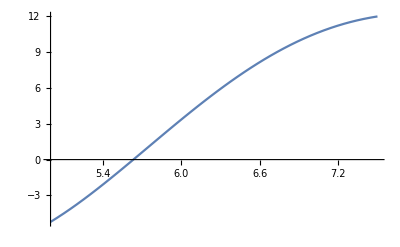

```mathematica
grf=Plot[f[x],{x,5,7.5}]
```

## в).

```mathematica
L1[x_]:=-2.09653*(x-5.2)/(5.6-5.2)-1.886*(x-5.6)/(5.2-5.6)
```

```mathematica
Expand[L1[x]]
```

0.85089-0.526325 x

```mathematica
L1[5.2]
L1[5.6]
```

-1.886

-2.09653

```mathematica
M2 = Abs[f''[5.2]]
```

5.1025

```mathematica
R1[x_]:=M2/(2!)Abs[(x-5.2)(x-5.6)]
```

```mathematica
R1[5.6]
```

0.

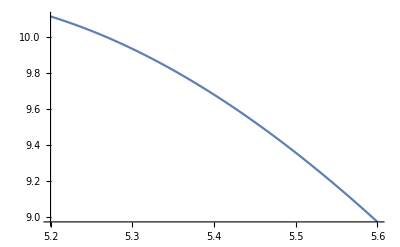

```mathematica
Plot[Abs[f'''[x]],{x,5.2,5.6}]
```

```mathematica
M3=Abs[f'''[5.6]]
```

8.9753

```mathematica
R2[x_]:=M3/(3!) Abs[(x-5.2) (x-5.4) (x-5.6)]
```

```mathematica
R2[5.4]
```

0.